# Tester notebook, just for experimenting

This is an earlier version of my work I saved just in case. I believe this is from February 2024

#### Rotation matrices applied to GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

```mathematica
(*visualizing matricies/ tensor*)
Rz[ϕ] //MatrixForm
P //MatrixForm
```

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

Applying the rotation matrix to all 3 polarizations. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

```mathematica
Simplify[Rz[ϕ].G.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ]-Sin[2 ϕ] | Cos[2 ϕ]+Sin[2 ϕ] | 0
Cos[2 ϕ]+Sin[2 ϕ] | -Cos[2 ϕ]+Sin[2 ϕ] | 0
0 | 0 | 0)

```mathematica
Simplify[Rz[ϕ].X.Transpose[Rz[ϕ]]] //MatrixForm
```

(-Sin[2 ϕ] | Cos[2 ϕ] | 0
Cos[2 ϕ] | Sin[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
Rx[α] //MatrixForm (*I think x should be by an angle α*)
Ry[α] //MatrixForm
```

(1 | 0 | 0
0 | Cos[α] | -Sin[α]
0 | Sin[α] | Cos[α])

(Cos[α] | 0 | Sin[α]
0 | 1 | 0
-Sin[α] | 0 | Cos[α])

#### Applying rotations:

Simplest case: Plus polarized wave rotated -α degrees about the x-axis and then ϕ degrees about the z-axis.

```mathematica
Simplify[Rz[ϕ].Rx[-α].P.Transpose[Rx[-α]].Transpose[Ry[ϕ]]] //MatrixForm
```

(Cos[ϕ]^2-Cos[α] Sin[α] Sin[ϕ]^2 | Cos[α]^2 Sin[ϕ] | -Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ]
Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ] | -Cos[α]^2 Cos[ϕ] | Cos[α] Cos[ϕ]^2 Sin[α]-Sin[ϕ]^2
-Sin[α]^2 Sin[ϕ] | Cos[α] Sin[α] | -Cos[ϕ] Sin[α]^2)

The most complex case: GW with a general plus polarization p and cross polarisation x rotated α degrees about the x-axis and then ϕ degrees about the z-axis.

```mathematica
Simplify[Rz[ϕ].Rx[-α].G.Transpose[Rx[-α]].Transpose[Ry[ϕ]]] //MatrixForm
```

(p Cos[ϕ]^2-x Cos[ϕ] (Cos[α]+Sin[α]) Sin[ϕ]-p Cos[α] Sin[α] Sin[ϕ]^2 | Cos[α] (x Cos[ϕ]+p Cos[α] Sin[ϕ]) | -x Cos[ϕ]^2 Sin[α]-p Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ]+x Cos[α] Sin[ϕ]^2
Cos[α] Cos[ϕ] (x Cos[ϕ]+p Sin[α] Sin[ϕ])+Sin[ϕ] (p Cos[ϕ]-x Sin[α] Sin[ϕ]) | Cos[α] (-p Cos[α] Cos[ϕ]+x Sin[ϕ]) | -Sin[ϕ] (x Cos[ϕ] Sin[α]+p Sin[ϕ])+Cos[α] Cos[ϕ] (p Cos[ϕ] Sin[α]-x Sin[ϕ])
-Sin[α] (x Cos[ϕ]+p Sin[α] Sin[ϕ]) | p Cos[α] Sin[α] | Sin[α] (-p Cos[ϕ] Sin[α]+x Sin[ϕ]))

#### Other variables

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is received
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP distance from GW source to photon
α angle between GW source and photon (measured up from GW propegation vector)
dP distance from Earth to the photon
tmin initial time the photon encounters the GW
n vector pointing to point on the sky where the photon is found

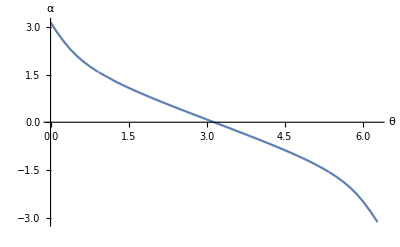

```mathematica
$Assumptions=dG>0&&h0>0&&tP>tG&&0<=θ<=2 π&&t∈Reals;
c= 1;
tG = 0;
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
A[dP_, dG_, θ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] 
(*DP[tP_, t_] := c(tP-t)*)
DP[tP_, t_] := If[tP>t,c(tP-t), 0] (*if tP > t*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP - 2 dG Cos[θ])
n[θ_] := {Sin[θ], 0, Cos[θ]}
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
Plot[A[5,3,θ], {θ,0,2π},AxesLabel->{"θ","α"}]
```

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t],dG,θ],{θ,0,2 π}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,5},{tP,0.1,2.5},{t,-3,2.5} ]
```

```mathematica
Tmin[tG, tP, dG,θ]
```

(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
Manipulate[Labeled[PolarPlot[Tmin[tG, tP, dG,θ],{θ,0,2 π}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,5},{tP,0.1,2.5}]
```

```mathematica
Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
```

√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])

```mathematica
Manipulate[Labeled[Plot[RP[dG,tP, t,θ],{t,-2,2}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", θ = ", NumberForm[θ, {3,2}]}],Top],{dG,0,5},{tP,0,2},{θ,0,2π}](*RP*) (*I think it looks good, not tested thoroughly tho*)
```

```mathematica
Manipulate[Labeled[Plot[{RG[dG,t],RP[dG,tP,t,θ]},{t,-2,2},PlotLegends->{"RG(dG, t)","RP(dG, tP, t, θ)"}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", θ = ",NumberForm[θ,{3,2}]}],Top],{dG,0,5},{tP,0,2},{θ,0,2 π}]
```

```mathematica
Solve[RG[dG,t] ==RP[dG,tP,t,θ],t]
```

{{t→(-tP^2+2 dG tP Cos[θ])/(2 (-dG-tP+dG Cos[θ]))}}

```mathematica
Manipulate[Labeled[PolarPlot[(-tP^2+2 dG tP Cos[θ])/(2 (-dG-tP+dG Cos[θ])),{θ,0,2 π}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,5},{tP,0.1,2.5}]
```

```mathematica
RG[dG_,t_]:= If[t>(-dG),dG+t,0];
```

```mathematica
Manipulate[Labeled[Plot[RG[dG,t],{t,-1,1}],Row[{"dG = ",NumberForm[dG,{3,2}]}],Top],{dG,0,1}]
```

```mathematica
Manipulate[Plot[DP[tP, t],{t,-3,3}],{dG,0,5},{tP,0,2},{θ,0,2π}] (*looks good*)
```

#### Metric in 2D simplification

Simplifying to 2D, in the plane of the Earth, GW source, and photon. Here, we are ignoring ϕ and only considering α.

```mathematica
P // MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = Ε[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵ] //MatrixForm
```

(Piecewise[{{1, t≥tP}, {(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0 | Piecewise[{{-1/2 Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]], t<tP}, {0, True}}]
0 | -1 | 0
Piecewise[{{-1/2 Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]], t<tP}, {0, True}}] | 0 | Piecewise[{{((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), t<tP}, {0, True}}])

```mathematica
H[t_, tP_, dG_, θ_] := 1/RP[dG,tP, t,θ] Ε[A[DP[tP,t], dG, θ]]
```

```mathematica
h = H[t,tP,dG,θ]; (*full expression for Subscript[h, ij], without multiplying by h0*)
```

```mathematica
FullSimplify[h] //MatrixForm
```

(Piecewise[{{1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t≥tP}, {(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), True}}] | 0 | Piecewise[{{-Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t<tP}, {0, True}}]
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
Piecewise[{{-Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t<tP}, {0, True}}] | 0 | Piecewise[{{((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}])

#### Simplifying metric representation

Simplifying  Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]

```mathematica
o = (t-tP) Sin[θ];
a = dG+(t-tP) Cos[θ];
```

```mathematica
hyp = Sqrt[a^2+o^2]
```

√((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2)

```mathematica
2*o/hyp*a/hyp (*Sin(2x) = 2CosxSinx*)
```

(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2)

```mathematica
sin2arctan = FullSimplify[(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2)] (*I graphed this against the original Sin[2ArcTan[]] and they look identical*)
```

(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
(sin2arctan)/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) (*Simplifying the expression that appears in the matrix*)
```

((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[ϵ] //MatrixForm
```

(Piecewise[{{1, t≥tP}, {(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0 | Piecewise[{{-1/2 Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]], t<tP}, {0, True}}]
0 | -1 | 0
Piecewise[{{-1/2 Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]], t<tP}, {0, True}}] | 0 | Piecewise[{{((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), t<tP}, {0, True}}])

```mathematica
ϵ = ({{Piecewise[{{1, t≥tP}, {(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}], 0, Piecewise[{{-1/2 sin2arctan, t<tP}, {0, True}}]}, {0, -1, 0}, {Piecewise[{{-1/2 sin2arctan, t<tP}, {0, True}}], 0, Piecewise[{{((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), t<tP}, {0, True}}]}})
```

{{Piecewise[{{1, t≥tP}, {(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}],0,Piecewise[{{-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), t<tP}, {0, True}}]},{0,-1,0},{Piecewise[{{-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), t<tP}, {0, True}}],0,Piecewise[{{((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), t<tP}, {0, True}}]}}

```mathematica
FullSimplify[h] //MatrixForm
```

(Piecewise[{{1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t≥tP}, {(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), True}}] | 0 | Piecewise[{{-Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t<tP}, {0, True}}]
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
Piecewise[{{-Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t<tP}, {0, True}}] | 0 | Piecewise[{{((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}])

```mathematica
h = ({{Piecewise[{{1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t≥tP}, {(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), True}}], 0, Piecewise[{{-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}]}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {Piecewise[{{-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}], 0, Piecewise[{{((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}]}})
```

{{Piecewise[{{1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), t≥tP}, {(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), True}}],0,Piecewise[{{-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}]},{0,-1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])),0},{Piecewise[{{-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}],0,Piecewise[{{((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {0, True}}]}}

#### Redshift

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h]] (*applying n^i n^j*)
```

Piecewise[{{(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), t<tP}, {Sin[θ]^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}]

```mathematica
(dG^2 Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))  (*taking the difference manually, updated tmin*)
```

-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2))

```mathematica
FullSimplify[-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2))]
```

(-1/dG+(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2

```mathematica
Manipulate[PolarPlot[(-1/dG+(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2,{θ,0,2 π}],{dG,0.1,3},{tP,0.1,3}]
```

```mathematica
(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))
```

```mathematica
FullSimplify[-1/2*(-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)^(3/2)))] (*full z expression*)
```

1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))

```mathematica
Z[θ_, dG_, tP_] := 1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))
```

```mathematica
Manipulate[PolarPlot[Z[θ,dG,tP] (*full z expression*),{θ,0,2 π}],{dG,0.1,3},{tP,0.1,2.5}]
```

```mathematica
Manipulate[Labeled[PolarPlot[Z[θ,dG,tP],{θ,0,2 π}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,1,2.5}]
```

z stabilizes when tP >> dG. The photon is received (measure after GW received) long after the light-travel time to the GW source.

```mathematica
FullSimplify[Z[θ,dG,tP]]
```

1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))

```mathematica
1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-dG tP Cos[θ]+tP^2/4)^(3/2))) ;(*z when tP>>dG*)
```

```mathematica
Manipulate[PolarPlot[1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2+tP^2/4-dG tP Cos[θ])^(3/2))),{θ,0,2 π}],{dG,0.01,3.604391290997247},{tP,0.01,3.604391290997247}]
```

```mathematica
zθMad = 1/4(1-Cos[θ]); (*Madison's equation for ϕ = 0*)
```

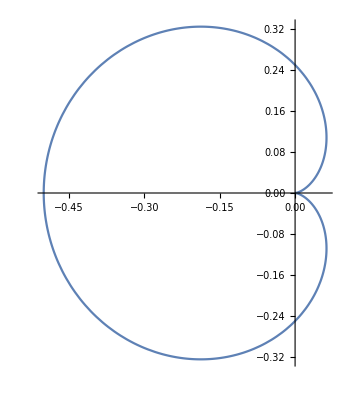

```mathematica
PolarPlot[zθMad,{θ,0,2 π}]
```

Next steps
- Write up in methods section while checking all steps
- Test for a few specific cases 
- Figure out how to get a graph to read off the values it has for dG and tP 

- Solve for angular displacements

Testing 3D case of a +-polarized wave with a general looking vector v = {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]}

```mathematica
intR = FullSimplify[n[θ].Transpose[n[θ].ϵr] *1/RP[dG,tP, t,θ]](*rotated integrand. applying n^i n^j and then applying 1/Rp*)
```

(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
ϵ3d = FullSimplify[Rz[ϕ].Ry[-α].P.Transpose[Ry[-α]]].Transpose[Rz[ϕ]] //MatrixForm (*plus polarized wave in 3D*)
```

(Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2 | Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | Cos[α] Cos[ϕ] Sin[α]
Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2 | Cos[α] Sin[α] Sin[ϕ]
Cos[α] Cos[ϕ] Sin[α] | Cos[α] Sin[α] Sin[ϕ] | Sin[α]^2)

```mathematica
FullSimplify[ϵ3d]
```

(Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2 | (1+Cos[α]^2) Cos[ϕ] Sin[ϕ] | Cos[α] Cos[ϕ] Sin[α]
(1+Cos[α]^2) Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2 | Cos[α] Sin[α] Sin[ϕ]
Cos[α] Cos[ϕ] Sin[α] | Cos[α] Sin[α] Sin[ϕ] | Sin[α]^2)

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]}
```

```mathematica
v[θ,ϕ].Transpose[v[θ,ϕ].ϵ3d] (*rotated integrand. applying v^i v^j and then applying 1/Rp*)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.Transpose[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.(Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2 | Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | Cos[α] Cos[ϕ] Sin[α]
Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2 | Cos[α] Sin[α] Sin[ϕ]
Cos[α] Cos[ϕ] Sin[α] | Cos[α] Sin[α] Sin[ϕ] | Sin[α]^2)]

```mathematica
FullSimplify[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.Transpose[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.({{Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2, Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ], Cos[α] Cos[ϕ] Sin[α]}, {Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ], -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2, Cos[α] Sin[α] Sin[ϕ]}, {Cos[α] Cos[ϕ] Sin[α], Cos[α] Sin[α] Sin[ϕ], Sin[α]^2}})]/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))]
```

Sin[α+θ]^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
FullSimplify[Sin[A[DP[tP,t], dG, θ]+θ]^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))]
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[(dG^2 Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))]
```

-Sin[θ]^2/dG+(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2))

```mathematica
Manipulate[PolarPlot[-Sin[θ]^2/dG+(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)),{θ,0,2 π}],{dG,0.1,3},{tP,-0.1,5}]
```

#### Other polarizations in 2D

Plus-polarized wave rotated through an angle ϕ

```mathematica
P //MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Rz[ϕ].P.Transpose[Rz[ϕ]] // MatrixForm
```

(Cos[ϕ]^2-Sin[ϕ]^2 | 2 Cos[ϕ] Sin[ϕ] | 0
2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Sin[ϕ]^2 | 0
0 | 0 | 0)

```mathematica
Εr[α_] := FullSimplify[Ry[-α].Rz[ϕ].P.Transpose[Rz[ϕ]].Transpose[Ry[-α]]] (*Polarization of a x GW at an angle α*)
Εr[α] //MatrixForm
```

(Cos[α]^2 Cos[2 ϕ] | Cos[α] Sin[2 ϕ] | Cos[α] Cos[2 ϕ] Sin[α]
Cos[α] Sin[2 ϕ] | -Cos[2 ϕ] | Sin[α] Sin[2 ϕ]
Cos[α] Cos[2 ϕ] Sin[α] | Sin[α] Sin[2 ϕ] | Cos[2 ϕ] Sin[α]^2)

```mathematica
ϵr = Εr[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵr] //MatrixForm
```

(((dG+(t-tP) Cos[θ])^2 Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | Piecewise[{{-Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 1/2 Cos[2 ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
Piecewise[{{-Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | -Cos[2 ϕ] | Sin[2 ϕ] Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]
1/2 Cos[2 ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | Sin[2 ϕ] Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] | ((t-tP)^2 Cos[2 ϕ] Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
intR = FullSimplify[n[θ].Transpose[n[θ].ϵr] *1/RP[dG,tP, t,θ]](*rotated integrand. applying n^i n^j and then applying 1/Rp*)
```

(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2)) ](*taking the difference manually*)
```

-(Cos[2 ϕ] Sin[θ]^2)/dG+(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2))

```mathematica
Zr[θ_, ϕ_, dG_, tP_] := -1/2*(-(Cos[2 ϕ] Sin[θ]^2)/dG+(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))
```

```mathematica
Manipulate[SphericalPlot3D[Zr[θ, ϕ, dG, tP],{θ,0,π},{ϕ,0,2 π}, PlotRange->All],{dG,0.01,10.},{tP,0.01,10.}]
```

```mathematica
(*why is this such a larger amplitude? This is not a 3D plot, it's for a general GW in a 2D geometry*)
```

```mathematica
zMad = 1/4*2Cos[2ϕ]*(1-Cos[θ]); (*Madison's full equation*)
```

```mathematica
SphericalPlot3D[zMad,{θ,0,π},{ϕ,0,2 π}, PlotRange->All]
```

-Graphics3D-

Cross-polarized wave

```mathematica
X //MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a x GW at an angle α*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = Εx[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵx] //MatrixForm
```

(0 | Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0
Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] | 0)

```mathematica
Εx = ϵx*1/RP[dG,tP, t,θ];
```

```mathematica
FullSimplify[n[θ].Transpose[n[θ].Εx] ](*applying n^i n^j and then applying 1/Rp*)
```

0

Getting 0 for some reason?

### Deflection angle

```mathematica
FullSimplify[h] //MatrixForm
```

(1/(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
Subscript[h, x]= D[DP[tP,t]Cos[θ] h,θ] ; (*x = dP Sin[θ] so dx = dP Cos[θ] dθ ?*) (*check Rp versus dp!!*)
Subscript[h, y]=0 ; 
Subscript[h, z]= D[-DP[tP,t]Sin[θ] h,θ] ; (*z = dP Cos[θ] so dz = -dP Sin[θ] dθ ?*)
FullSimplify[Subscript[h, x]] //MatrixForm
FullSimplify[Subscript[h, z]] //MatrixForm
```

(((t-tP) (dG+(t-tP) Cos[θ]) (3 (dG^2+(t-tP)^2) (t-tP) Cos[θ]+dG (dG^2+3 (t-tP)^2+2 (t-tP)^2 Cos[2 θ])) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | ((t-tP)^2 ((7 dG^2+(t-tP)^2) (t-tP) Cos[θ]+4 dG Cos[2 θ] (dG^2+2 (t-tP)^2+(t-tP)^2 Cos[2 θ])+(5 dG^2+3 (t-tP)^2) (t-tP) Cos[3 θ]))/(4 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | (-t+tP) Sin[θ] | 0
((t-tP)^2 ((7 dG^2+(t-tP)^2) (t-tP) Cos[θ]+4 dG Cos[2 θ] (dG^2+2 (t-tP)^2+(t-tP)^2 Cos[2 θ])+(5 dG^2+3 (t-tP)^2) (t-tP) Cos[3 θ]))/(4 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | -((t-tP)^3 (6 dG (t-tP) Cos[θ]+(dG^2+(t-tP)^2) (1+3 Cos[2 θ])+2 dG (t-tP) Cos[3 θ]) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

(((t-tP) (Cos[θ]+((t-tP)^2 (-2 t+2 tP-dG Cos[θ]+(t-tP) Cos[θ]^2) Sin[θ]^2)/(dG+(t-tP) Cos[θ])^3))/((1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)^2) | 0 | -((t-tP)^2 (2 dG (2 dG^2+5 (t-tP)^2) Cos[θ]+(t-tP) (7 dG^2+(t-tP)^2+(5 dG^2+3 (t-tP)^2) Cos[2 θ]+2 dG (t-tP) Cos[3 θ])) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | (-t+tP) Cos[θ] | 0
-((t-tP)^2 (2 dG (2 dG^2+5 (t-tP)^2) Cos[θ]+(t-tP) (7 dG^2+(t-tP)^2+(5 dG^2+3 (t-tP)^2) Cos[2 θ]+2 dG (t-tP) Cos[3 θ])) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | ((t-tP)^3 (3 (dG^2+(t-tP)^2) Cos[θ]+2 dG (t-tP) (2+Cos[2 θ])) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

```mathematica
Integrate[Subscript[h, x],{t,Tmin[tG, tP, dG,θ],tP}]
```

ConditionalExpression[(h0 (2 dG^2+2 dG tP+2 dG^2 Cos[θ]-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ])) (Cos[θ]+ⅈ Sin[θ]))/(dG (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])), ]

$Aborted

Piecewise[{{{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,((-t+tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))},{0,1,0},{((t-tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))}}.{Cos[2 ϕ] Sin[θ]^2}.{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,((t-tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))},{0,1,0},{((-t+tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))}}, (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {{{1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,((t-tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))},{0,1,0},{((-t+tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))}}.{Cos[2 ϕ] Sin[θ]^2}.{{1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,((-t+tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))},{0,1,0},{((t-tP) Sin[θ])/((dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)),0,1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2))}}, True}}]